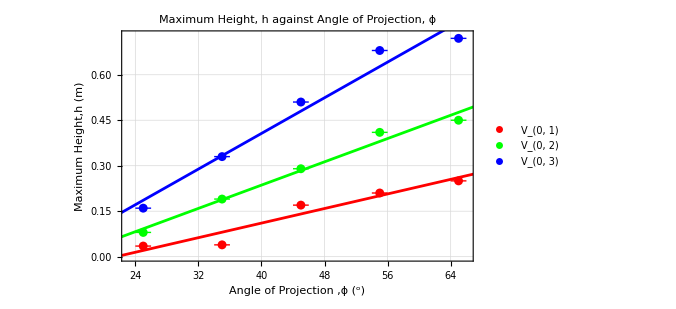
-Graphics-
V_(0, 1): y==0.00601 x-0.12965
V_(0, 2): y==0.0096 x-0.148
V_(0, 3): y==0.0147 x-0.1815

```mathematica
(*Define the datasets*)V1={{25,0.035},{35,0.039},{45,0.170},{55,0.210},{65,0.250}};
V2={{25,0.080},{35,0.190},{45,0.290},{55,0.410},{65,0.450}};
V3={{25,0.160},{35,0.330},{45,0.510},{55,0.680},{65,0.720}};

V1error={
{Around[25,1],Around[0.035,0.01]},{Around[35,1],Around[0.039,0.01]},{Around[45,1],Around[0.170,0.01]},{Around[55,1],Around[0.210,0.01]},{Around[65,1],Around[0.250,0.01]}};
V2error={
{Around[25,1],Around[0.080,0.01]},{Around[35,1],Around[0.190,0.01]},{Around[45,1],Around[0.290,0.01]},{Around[55,1],Around[0.410,0.01]},{Around[65,1],Around[0.450,0.01]}};
V3error={
{Around[25,1],Around[0.160,0.01]},{Around[35,1],Around[0.330,0.01]},{Around[45,1],Around[0.510,0.01]},{Around[55,1],Around[0.680,0.01]},{Around[65,1],Around[0.720,0.01]}};

(*Fit linear models to the data*)
fitV1=LinearModelFit[V1,x,x];
fitV2=LinearModelFit[V2,x,x];
fitV3=LinearModelFit[V3,x,x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fitV1["BestFit"]]];
eq2=ToString[TraditionalForm[y==fitV2["BestFit"]]];
eq3=ToString[TraditionalForm[y==fitV3["BestFit"]]];

(*Plot the data and the best-fit lines*)
Column[{combinedPlot=Show[ListPlot[{V1error,V2error,V3error},PlotStyle->{Red,Green,Blue},PlotLegends->{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 2\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 3\)]\)"}],Plot[{fitV1[x],fitV2[x],fitV3[x]},{x,0,90},PlotStyle->{Red,Green,Blue},PlotRange->{{0,90},Automatic}],Frame->True,FrameLabel->{"Angle of Projection ,ϕ (^o)","Maximum Height,h (m)"},GridLines->Automatic,PlotLabel->"Maximum Height, h against Angle of Projection, ϕ",ImageSize->500],Column[{Row[{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\): ",eq1}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 2\)]\): ",eq2}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 3\)]\): ",eq3}]}]}]
```

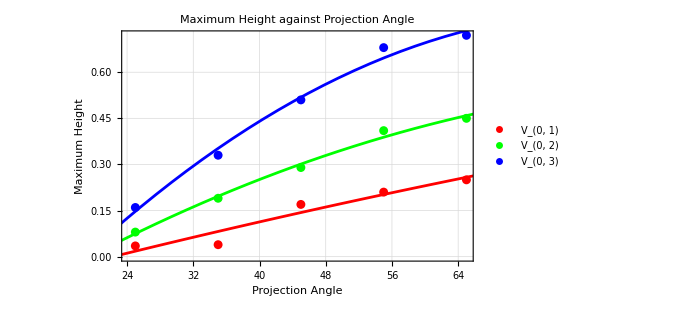
-Graphics-
V_(0, 1): y==-0.0000135714 x^2+0.00723143 x-0.154418
V_(0, 2): y==-0.0000857143 x^2+0.0173143 x-0.304429
V_(0, 3): y==-0.000192857 x^2+0.0320571 x-0.533464

```mathematica
(*Define the datasets*)V1={{25,0.035},{35,0.039},{45,0.170},{55,0.210},{65,0.250}};
V2={{25,0.080},{35,0.190},{45,0.290},{55,0.410},{65,0.450}};
V3={{25,0.160},{35,0.330},{45,0.510},{55,0.680},{65,0.720}};

(*Fit quadratic models to the data*)
fitV1=NonlinearModelFit[V1,a*x^2+b*x+c,{a,b,c},x];
fitV2=NonlinearModelFit[V2,a*x^2+b*x+c,{a,b,c},x];
fitV3=NonlinearModelFit[V3,a*x^2+b*x+c,{a,b,c},x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fitV1["BestFit"]]];
eq2=ToString[TraditionalForm[y==fitV2["BestFit"]]];
eq3=ToString[TraditionalForm[y==fitV3["BestFit"]]];

(*Plot the data and the best-fit curves*)
Column[{combinedPlot=Show[ListPlot[{V1,V2,V3},PlotStyle->{Red,Green,Blue},PlotLegends->{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 2\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 3\)]\)"}],Plot[{fitV1[x],fitV2[x],fitV3[x]},{x,0,90},PlotStyle->{Red,Green,Blue},PlotRange->{{0,90},Automatic}],Frame->True,FrameLabel->{"Projection Angle","Maximum Height"},GridLines->Automatic,PlotLabel->"Maximum Height against Projection Angle",ImageSize->500],Column[{Row[{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\): ",eq1}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 2\)]\): ",eq2}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 3\)]\): ",eq3}]}]}]
```

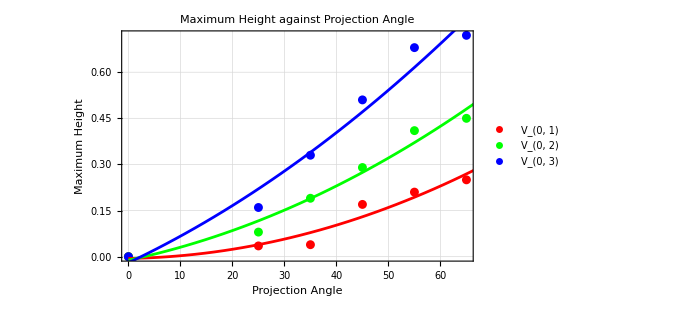
-Graphics-
V_(0, 1): y==0.0000609403 x^2+0.000268156 x-0.00571597
V_(0, 2): y==0.0000611825 x^2+0.00358648 x-0.0112688
V_(0, 3): y==0.000064557 x^2+0.00800127 x-0.0197468

```mathematica
(*Define the datasets*)
V1={{0,0},{25,0.035},{35,0.039},{45,0.170},{55,0.210},{65,0.250}};
V2={{0,0},{25,0.080},{35,0.190},{45,0.290},{55,0.410},{65,0.450}};
V3={{0,0},{25,0.160},{35,0.330},{45,0.510},{55,0.680},{65,0.720}};

(*Fit quadratic models to the data*)
fitV1=NonlinearModelFit[V1,a*x^2+b*x+c,{a,b,c},x];
fitV2=NonlinearModelFit[V2,a*x^2+b*x+c,{a,b,c},x];
fitV3=NonlinearModelFit[V3,a*x^2+b*x+c,{a,b,c},x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fitV1["BestFit"]]];
eq2=ToString[TraditionalForm[y==fitV2["BestFit"]]];
eq3=ToString[TraditionalForm[y==fitV3["BestFit"]]];

(*Plot the data and the best-fit curves*)
Column[{combinedPlot=Show[ListPlot[{V1,V2,V3},PlotStyle->{Red,Green,Blue},PlotLegends->{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 2\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 3\)]\)"}],Plot[{fitV1[x],fitV2[x],fitV3[x]},{x,0,90},PlotStyle->{Red,Green,Blue},PlotRange->{{0,90},Automatic}],Frame->True,FrameLabel->{"Projection Angle","Maximum Height"},GridLines->Automatic,PlotLabel->"Maximum Height against Projection Angle",ImageSize->500],Column[{Row[{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\): ",eq1}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 2\)]\): ",eq2}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 3\)]\): ",eq3}]}]}]
```

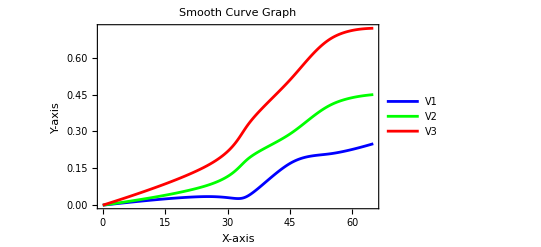

```mathematica
V1={{0,0},{25,0.035},{35,0.039},{45,0.170},{55,0.210},{65,0.250}};
V2={{0,0},{25,0.080},{35,0.190},{45,0.290},{55,0.410},{65,0.450}};
V3={{0,0},{25,0.160},{35,0.330},{45,0.510},{55,0.680},{65,0.720}};

ListLinePlot[{V1,V2,V3},InterpolationOrder->3,MeshFunctions->{#1&},MeshStyle->Red,PlotStyle->{Blue,Green,Red},PlotLegends->{"V1","V2","V3"},Frame->True,FrameLabel->{"X-axis","Y-axis"},PlotLabel->"Smooth Curve Graph"]
```